```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])- t22(hop[a[3],a[6]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.3,cj->U/5,U->4,t23->x t22,t22->0.3}
```

{Δ→0.3,𝒿→U/5,U→4,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

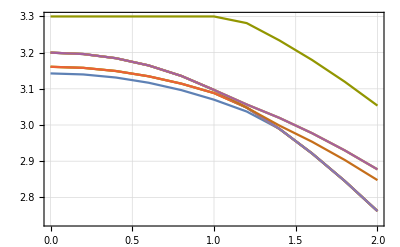

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

0.0000657264

1

0.000930535

1

0.00352274

1

0.00783439

1

0.013848

1

0.0215306

1

0.0308274

1

0.0416541

1

0.053892

1

0.0673852

1

0.0819413

1

0.0973372

1

0.113328

1

0.12966

1

5.53672

1

5.46111

1

5.38445

1

5.30817

1

5.23345

1

5.16121

1

5.09212

2

1.99995

2

1.9997

2

1.99894

2

1.9977

2

1.99598

2

1.99382

2

1.99125

2

1.98831

2

1.98502

2

1.98141

2

1.97752

2

1.97337

2

5.67844

2

5.60969

2

5.53672

2

5.46111

2

5.38445

2

5.30817

2

5.23345

2

5.16121

2

5.09212

3

1.99995

3

1.9997

3

1.99894

3

1.9977

3

1.99598

3

1.99382

3

1.99125

3

1.98831

3

1.98502

3

1.98141

3

1.97752

3

1.97337

3

5.67844

3

5.60969

3

5.53672

3

5.46111

3

5.38445

3

5.30817

3

5.23345

3

5.16121

3

5.09212

4

1.99995

4

1.9997

4

1.99894

4

1.9977

4

1.99598

4

1.99382

4

1.99125

4

1.98831

4

1.98502

4

1.98141

4

1.97752

4

1.97337

4

5.67844

4

5.60969

4

5.53672

4

5.46111

4

5.38445

4

5.30817

4

5.23345

4

5.16121

4

5.09212

5

6.

5

5.99887

5

5.99532

5

5.98896

5

5.97912

5

5.96494

5

5.94546

5

5.9197

5

5.88681

5

5.8462

5

5.79767

5

5.74149

5

5.67844

5

5.60969

5

5.53672

5

5.46111

5

5.38445

5

5.30817

5

5.23345

5

5.16121

5

5.09212

6

6.

6

5.99887

6

5.99532

6

5.98896

6

5.97912

6

5.96494

6

5.94546

6

5.9197

6

5.88681

6

5.8462

6

5.79767

6

5.74149

6

5.67844

6

5.60969

6

0.146082

6

0.162361

6

0.178289

6

0.193692

6

0.208434

6

0.222413

6

0.235566

7

6.

7

5.99887

7

5.99532

7

5.98896

7

5.97912

7

5.96494

7

5.94546

7

5.9197

7

5.88681

7

5.8462

7

5.79767

7

5.74149

7

1.96898

7

1.96437

7

1.95952

7

1.95446

7

1.94917

7

1.94365

7

1.93788

7

1.93185

7

1.92554

8

6.

8

5.99887

8

5.99532

8

5.98896

8

5.97912

8

5.96494

8

5.94546

8

5.9197

8

5.88681

8

5.8462

8

5.79767

8

5.74149

8

1.96898

8

1.96437

8

1.95952

8

1.95446

8

1.94917

8

1.94365

8

1.93788

8

1.93185

8

1.92554

9

6.

9

5.99887

9

5.99532

9

5.98896

9

5.97912

9

5.96494

9

5.94546

9

5.9197

9

5.88681

9

5.8462

9

5.79767

9

5.74149

9

1.96898

9

1.96437

9

1.95952

9

1.95446

9

1.94917

9

1.94365

9

1.93788

9

1.93185

9

1.92554

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

0.7239

10

0.721124

10

0.718494

10

0.716035

10

0.713764

10

0.711693

10

0.70983

10

0.708177

10

0.706735

```mathematica
data1//MatrixForm
```

(1 | 0. | 0.0000657264 | 3.14258
1 | 0.1 | 0.000930535 | 3.14187
1 | 0.2 | 0.00352274 | 3.13975
1 | 0.3 | 0.00783439 | 3.13619
1 | 0.4 | 0.013848 | 3.1312
1 | 0.5 | 0.0215306 | 3.12475
1 | 0.6 | 0.0308274 | 3.11682
1 | 0.7 | 0.0416541 | 3.1074
1 | 0.8 | 0.053892 | 3.09645
1 | 0.9 | 0.0673852 | 3.08398
1 | 1. | 0.0819413 | 3.06996
1 | 1.1 | 0.0973372 | 3.0544
1 | 1.2 | 0.113328 | 3.03729
1 | 1.3 | 0.12966 | 3.01864
1 | 1.4 | 5.53672 | 2.98942
1 | 1.5 | 5.46111 | 2.95651
1 | 1.6 | 5.38445 | 2.92142
1 | 1.7 | 5.30817 | 2.88428
1 | 1.8 | 5.23345 | 2.84524
1 | 1.9 | 5.16121 | 2.80446
1 | 2. | 5.09212 | 2.7621
2 | 0. | 1.99995 | 3.1609
2 | 0.1 | 1.9997 | 3.16016
2 | 0.2 | 1.99894 | 3.15797
2 | 0.3 | 1.9977 | 3.15431
2 | 0.4 | 1.99598 | 3.1492
2 | 0.5 | 1.99382 | 3.14263
2 | 0.6 | 1.99125 | 3.13462
2 | 0.7 | 1.98831 | 3.12517
2 | 0.8 | 1.98502 | 3.1143
2 | 0.9 | 1.98141 | 3.102
2 | 1. | 1.97752 | 3.0883
2 | 1.1 | 1.97337 | 3.0732
2 | 1.2 | 5.67844 | 3.04816
2 | 1.3 | 5.60969 | 3.02
2 | 1.4 | 5.53672 | 2.98942
2 | 1.5 | 5.46111 | 2.95651
2 | 1.6 | 5.38445 | 2.92142
2 | 1.7 | 5.30817 | 2.88428
2 | 1.8 | 5.23345 | 2.84524
2 | 1.9 | 5.16121 | 2.80446
2 | 2. | 5.09212 | 2.7621
3 | 0. | 1.99995 | 3.1609
3 | 0.1 | 1.9997 | 3.16016
3 | 0.2 | 1.99894 | 3.15797
3 | 0.3 | 1.9977 | 3.15431
3 | 0.4 | 1.99598 | 3.1492
3 | 0.5 | 1.99382 | 3.14263
3 | 0.6 | 1.99125 | 3.13462
3 | 0.7 | 1.98831 | 3.12517
3 | 0.8 | 1.98502 | 3.1143
3 | 0.9 | 1.98141 | 3.102
3 | 1. | 1.97752 | 3.0883
3 | 1.1 | 1.97337 | 3.0732
3 | 1.2 | 5.67844 | 3.04816
3 | 1.3 | 5.60969 | 3.02
3 | 1.4 | 5.53672 | 2.98942
3 | 1.5 | 5.46111 | 2.95651
3 | 1.6 | 5.38445 | 2.92142
3 | 1.7 | 5.30817 | 2.88428
3 | 1.8 | 5.23345 | 2.84524
3 | 1.9 | 5.16121 | 2.80446
3 | 2. | 5.09212 | 2.7621
4 | 0. | 1.99995 | 3.1609
4 | 0.1 | 1.9997 | 3.16016
4 | 0.2 | 1.99894 | 3.15797
4 | 0.3 | 1.9977 | 3.15431
4 | 0.4 | 1.99598 | 3.1492
4 | 0.5 | 1.99382 | 3.14263
4 | 0.6 | 1.99125 | 3.13462
4 | 0.7 | 1.98831 | 3.12517
4 | 0.8 | 1.98502 | 3.1143
4 | 0.9 | 1.98141 | 3.102
4 | 1. | 1.97752 | 3.0883
4 | 1.1 | 1.97337 | 3.0732
4 | 1.2 | 5.67844 | 3.04816
4 | 1.3 | 5.60969 | 3.02
4 | 1.4 | 5.53672 | 2.98942
4 | 1.5 | 5.46111 | 2.95651
4 | 1.6 | 5.38445 | 2.92142
4 | 1.7 | 5.30817 | 2.88428
4 | 1.8 | 5.23345 | 2.84524
4 | 1.9 | 5.16121 | 2.80446
4 | 2. | 5.09212 | 2.7621
5 | 0. | 6. | 3.2
5 | 0.1 | 5.99887 | 3.19905
5 | 0.2 | 5.99532 | 3.19619
5 | 0.3 | 5.98896 | 3.19139
5 | 0.4 | 5.97912 | 3.18459
5 | 0.5 | 5.96494 | 3.1757
5 | 0.6 | 5.94546 | 3.16465
5 | 0.7 | 5.9197 | 3.15134
5 | 0.8 | 5.88681 | 3.13568
5 | 0.9 | 5.8462 | 3.11757
5 | 1. | 5.79767 | 3.09697
5 | 1.1 | 5.74149 | 3.07383
5 | 1.2 | 5.67844 | 3.04816
5 | 1.3 | 5.60969 | 3.02
5 | 1.4 | 5.53672 | 2.98942
5 | 1.5 | 5.46111 | 2.95651
5 | 1.6 | 5.38445 | 2.92142
5 | 1.7 | 5.30817 | 2.88428
5 | 1.8 | 5.23345 | 2.84524
5 | 1.9 | 5.16121 | 2.80446
5 | 2. | 5.09212 | 2.7621
6 | 0. | 6. | 3.2
6 | 0.1 | 5.99887 | 3.19905
6 | 0.2 | 5.99532 | 3.19619
6 | 0.3 | 5.98896 | 3.19139
6 | 0.4 | 5.97912 | 3.18459
6 | 0.5 | 5.96494 | 3.1757
6 | 0.6 | 5.94546 | 3.16465
6 | 0.7 | 5.9197 | 3.15134
6 | 0.8 | 5.88681 | 3.13568
6 | 0.9 | 5.8462 | 3.11757
6 | 1. | 5.79767 | 3.09697
6 | 1.1 | 5.74149 | 3.07383
6 | 1.2 | 5.67844 | 3.04816
6 | 1.3 | 5.60969 | 3.02
6 | 1.4 | 0.146082 | 2.99848
6 | 1.5 | 0.162361 | 2.97683
6 | 1.6 | 0.178289 | 2.95373
6 | 1.7 | 0.193692 | 2.92921
6 | 1.8 | 0.208434 | 2.90333
6 | 1.9 | 0.222413 | 2.87612
6 | 2. | 0.235566 | 2.84765
7 | 0. | 6. | 3.2
7 | 0.1 | 5.99887 | 3.19905
7 | 0.2 | 5.99532 | 3.19619
7 | 0.3 | 5.98896 | 3.19139
7 | 0.4 | 5.97912 | 3.18459
7 | 0.5 | 5.96494 | 3.1757
7 | 0.6 | 5.94546 | 3.16465
7 | 0.7 | 5.9197 | 3.15134
7 | 0.8 | 5.88681 | 3.13568
7 | 0.9 | 5.8462 | 3.11757
7 | 1. | 5.79767 | 3.09697
7 | 1.1 | 5.74149 | 3.07383
7 | 1.2 | 1.96898 | 3.05673
7 | 1.3 | 1.96437 | 3.03888
7 | 1.4 | 1.95952 | 3.01969
7 | 1.5 | 1.95446 | 2.99917
7 | 1.6 | 1.94917 | 2.97734
7 | 1.7 | 1.94365 | 2.95422
7 | 1.8 | 1.93788 | 2.92982
7 | 1.9 | 1.93185 | 2.90418
7 | 2. | 1.92554 | 2.87732
8 | 0. | 6. | 3.2
8 | 0.1 | 5.99887 | 3.19905
8 | 0.2 | 5.99532 | 3.19619
8 | 0.3 | 5.98896 | 3.19139
8 | 0.4 | 5.97912 | 3.18459
8 | 0.5 | 5.96494 | 3.1757
8 | 0.6 | 5.94546 | 3.16465
8 | 0.7 | 5.9197 | 3.15134
8 | 0.8 | 5.88681 | 3.13568
8 | 0.9 | 5.8462 | 3.11757
8 | 1. | 5.79767 | 3.09697
8 | 1.1 | 5.74149 | 3.07383
8 | 1.2 | 1.96898 | 3.05673
8 | 1.3 | 1.96437 | 3.03888
8 | 1.4 | 1.95952 | 3.01969
8 | 1.5 | 1.95446 | 2.99917
8 | 1.6 | 1.94917 | 2.97734
8 | 1.7 | 1.94365 | 2.95422
8 | 1.8 | 1.93788 | 2.92982
8 | 1.9 | 1.93185 | 2.90418
8 | 2. | 1.92554 | 2.87732
9 | 0. | 6. | 3.2
9 | 0.1 | 5.99887 | 3.19905
9 | 0.2 | 5.99532 | 3.19619
9 | 0.3 | 5.98896 | 3.19139
9 | 0.4 | 5.97912 | 3.18459
9 | 0.5 | 5.96494 | 3.1757
9 | 0.6 | 5.94546 | 3.16465
9 | 0.7 | 5.9197 | 3.15134
9 | 0.8 | 5.88681 | 3.13568
9 | 0.9 | 5.8462 | 3.11757
9 | 1. | 5.79767 | 3.09697
9 | 1.1 | 5.74149 | 3.07383
9 | 1.2 | 1.96898 | 3.05673
9 | 1.3 | 1.96437 | 3.03888
9 | 1.4 | 1.95952 | 3.01969
9 | 1.5 | 1.95446 | 2.99917
9 | 1.6 | 1.94917 | 2.97734
9 | 1.7 | 1.94365 | 2.95422
9 | 1.8 | 1.93788 | 2.92982
9 | 1.9 | 1.93185 | 2.90418
9 | 2. | 1.92554 | 2.87732
10 | 0. | 3.75 | 3.3
10 | 0.1 | 3.75 | 3.3
10 | 0.2 | 3.75 | 3.3
10 | 0.3 | 3.75 | 3.3
10 | 0.4 | 3.75 | 3.3
10 | 0.5 | 3.75 | 3.3
10 | 0.6 | 3.75 | 3.3
10 | 0.7 | 3.75 | 3.3
10 | 0.8 | 3.75 | 3.3
10 | 0.9 | 3.75 | 3.3
10 | 1. | 3.75 | 3.3
10 | 1.1 | 3.75 | 3.3
10 | 1.2 | 0.7239 | 3.28163
10 | 1.3 | 0.721124 | 3.25853
10 | 1.4 | 0.718494 | 3.23381
10 | 1.5 | 0.716035 | 3.20752
10 | 1.6 | 0.713764 | 3.17969
10 | 1.7 | 0.711693 | 3.15035
10 | 1.8 | 0.70983 | 3.11953
10 | 1.9 | 0.708177 | 3.08726
10 | 2. | 0.706735 | 3.05357)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;14,1;;4]];
tmp02=data1[[120;;126,1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e0data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[22;;33,1;;4]];
tmp02=data1[[181;;189,1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[15;;21,1;;4]];
tmp02=data1[[106;;119,1;;4]];
tmp03=Flatten[{tmp02,tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.14258 | 0.0000657264
0.1 | 3.14187 | 0.000930535
0.2 | 3.13975 | 0.00352274
0.3 | 3.13619 | 0.00783439
0.4 | 3.1312 | 0.013848
0.5 | 3.12475 | 0.0215306
0.6 | 3.11682 | 0.0308274
0.7 | 3.1074 | 0.0416541
0.8 | 3.09645 | 0.053892
0.9 | 3.08398 | 0.0673852
1. | 3.06996 | 0.0819413
1.1 | 3.0544 | 0.0973372
1.2 | 3.03729 | 0.113328
1.3 | 3.01864 | 0.12966
1.4 | 2.99848 | 0.146082
1.5 | 2.97683 | 0.162361
1.6 | 2.95373 | 0.178289
1.7 | 2.92921 | 0.193692
1.8 | 2.90333 | 0.208434
1.9 | 2.87612 | 0.222413
2. | 2.84765 | 0.235566)

(0. | 3.1609 | 1.99995
0.1 | 3.16016 | 1.9997
0.2 | 3.15797 | 1.99894
0.3 | 3.15431 | 1.9977
0.4 | 3.1492 | 1.99598
0.5 | 3.14263 | 1.99382
0.6 | 3.13462 | 1.99125
0.7 | 3.12517 | 1.98831
0.8 | 3.1143 | 1.98502
0.9 | 3.102 | 1.98141
1. | 3.0883 | 1.97752
1.1 | 3.0732 | 1.97337
1.2 | 3.05673 | 1.96898
1.3 | 3.03888 | 1.96437
1.4 | 3.01969 | 1.95952
1.5 | 2.99917 | 1.95446
1.6 | 2.97734 | 1.94917
1.7 | 2.95422 | 1.94365
1.8 | 2.92982 | 1.93788
1.9 | 2.90418 | 1.93185
2. | 2.87732 | 1.92554)

(0. | 3.2 | 6.
0.1 | 3.19905 | 5.99887
0.2 | 3.19619 | 5.99532
0.3 | 3.19139 | 5.98896
0.4 | 3.18459 | 5.97912
0.5 | 3.1757 | 5.96494
0.6 | 3.16465 | 5.94546
0.7 | 3.15134 | 5.9197
0.8 | 3.13568 | 5.88681
0.9 | 3.11757 | 5.8462
1. | 3.09697 | 5.79767
1.1 | 3.07383 | 5.74149
1.2 | 3.04816 | 5.67844
1.3 | 3.02 | 5.60969
1.4 | 2.98942 | 5.53672
1.5 | 2.95651 | 5.46111
1.6 | 2.92142 | 5.38445
1.7 | 2.88428 | 5.30817
1.8 | 2.84524 | 5.23345
1.9 | 2.80446 | 5.16121
2. | 2.7621 | 5.09212)

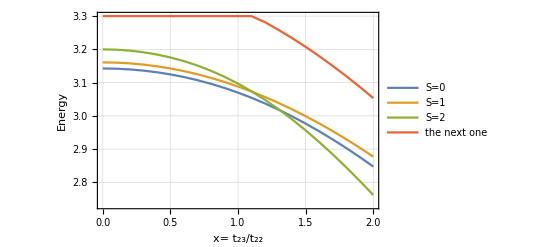

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

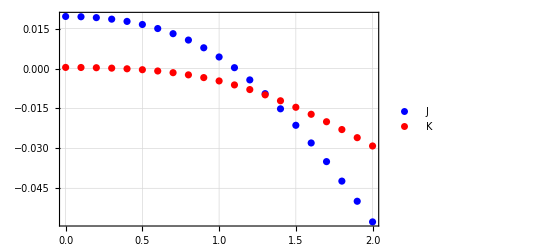

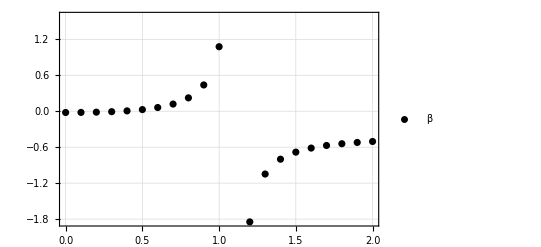

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```